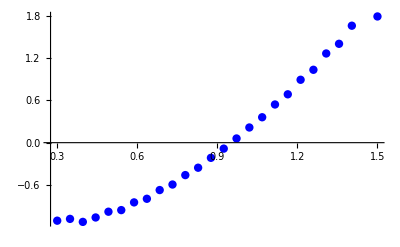

```mathematica
dataset = ({{0.3, -1.10525}, {0.348, -1.07996}, {0.396, -1.1225}, {0.444, -1.05986}, {0.492, -0.978257}, {0.54, -0.955469}, {0.588, -0.846209}, {0.636, -0.794931}, {0.684, -0.671395}, {0.732, -0.593028}, {0.78, -0.459459}, {0.828, -0.354877}, {0.876, -0.214726}, {0.924, -0.0844691}, {0.972, 0.0593841}, {1.02, 0.215}, {1.068, 0.360091}, {1.116, 0.540909}, {1.164, 0.685119}, {1.212, 0.891074}, {1.26, 1.03252}, {1.308, 1.26364}, {1.356, 1.40065}, {1.404, 1.65703}, {1.5, 1.7881}});
h= 0.048;a = 0.3;b = 1.5;dots = (b-a)/h;
appfunc=Interpolation[dataset];
Plot[appfunc]
datasetTable = Table[{dataset[[i,1]],dataset[[i,2]]}, {i,1,dots}];
dotsPlot=ListPlot[dataset,PlotStyle->{PointSize[0.015],Blue}];
Show[dotsPlot]
```

### Задание 1

```mathematica
polynomial = InterpolatingPolynomial[datasetTable, x];
plot = Plot[polynomial, {x,1,2}, PlotStyle->{Red}];
Expand[polynomial]
```

2.38656×10^10-7.99029×10^11 x+1.26697×10^13 x^2-1.26651×10^14 x^3+8.96309×10^14 x^4-4.78038×10^15 x^5+1.99697×10^16 x^6-6.70377×10^16 x^7+1.84086×10^17 x^8-4.18707×10^17 x^9+7.95762×10^17 x^10-1.27106×10^18 x^11+1.71212×10^18 x^12-1.94729×10^18 x^13+1.8685×10^18 x^14-1.5081×10^18 x^15+1.01835×10^18 x^16-5.70527×10^17 x^17+2.62011×10^17 x^18-9.69378×10^16 x^19+2.81736×10^16 x^20-6.19155×10^15 x^21+9.66929×10^14 x^22-9.55969×10^13 x^23+4.49674×10^12 x^24

```mathematica
datasetTablefor12 = Table[{dataset[[i,1]],dataset[[i,2]]},{i,1,25,2}];
polynomialfor12 = InterpolatingPolynomial[datasetTablefor12, x];
plotfor12 = Plot[polynomialfor12, {x,1,2}, PlotStyle->{Green}];
Expand[polynomialfor12]
```

287.455-4604.18 x+32759.2 x^2-137846. x^3+382879. x^4-740816. x^5+1.02533×10^6 x^6-1.02405×10^6 x^7+733242. x^8-367392. x^9+122365. x^10-24339.8 x^11+2187.87 x^12

```mathematica
datasetTablefor8 = Table[{dataset[[i,1]],dataset[[i,2]]},{i,1,25,3}];
polynomialfor8 = InterpolatingPolynomial[datasetTablefor8, x];
plotfor8 = Plot[polynomialfor8, {x,1,2}, PlotStyle->{Red}];
Expand[polynomialfor8]
```

22.5259-262.881 x+1208.01 x^2-3017.1 x^3+4503.58 x^4-4119.39 x^5+2260.83 x^6-682.259 x^7+86.8241 x^8

```mathematica
ind = {1,6,11,16,21,25};
datasetTablefor5 = Table[{dataset[[ind[[i]],1]],dataset[[ind[[i]],2]]},{i,1,6}];
polynomialfor5 = InterpolatingPolynomial[datasetTablefor5, x];
plotfor5 = Plot[polynomialfor5, {x,1,2},PlotStyle->{Orange}];
Expand[polynomialfor5]
```

0.17759-9.37965 x+23.2574 x^2-24.7314 x^3+13.9892 x^4-3.16065 x^5

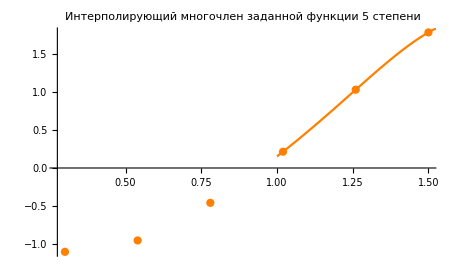

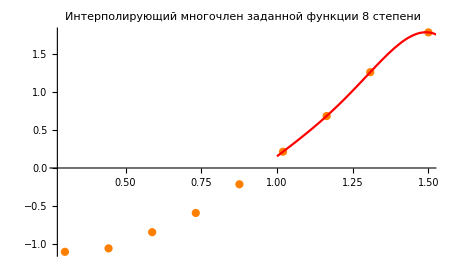

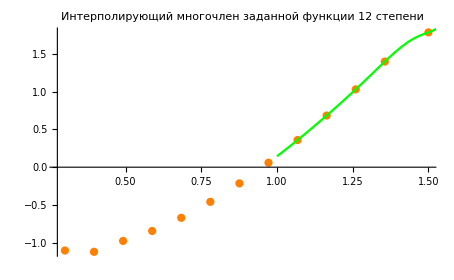

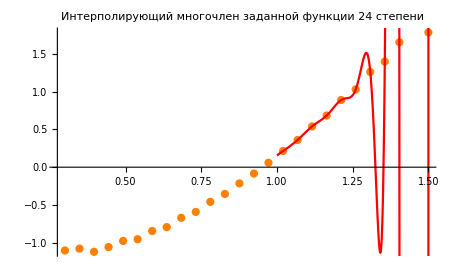

```mathematica
Show[ListPlot[datasetTablefor5, PlotStyle->{PointSize[0.013],Orange}],plotfor5, PlotLabel->"Интерполирующий многочлен заданной функции 5 степени"]
Show[ListPlot[datasetTablefor8, PlotStyle->{PointSize[0.013],Orange}],plotfor8,PlotLabel->"Интерполирующий многочлен заданной функции 8 степени"]
Show[ListPlot[datasetTablefor12, PlotStyle->{PointSize[0.013],Orange}],plotfor12, PlotLabel->"Интерполирующий многочлен заданной функции 12 степени"]
Show[ListPlot[datasetTable, PlotStyle->{PointSize[0.013],Orange}],plot, PlotLabel->"Интерполирующий многочлен заданной функции 24 степени"]
```

```mathematica
difffor24 = Table[{funcTable[[i,1]], (polynomial /. x-> datasetTable[[i,1]])- datasetTable[[i,2]]}, {i,1,dots}];
difffor12 = Table[{funcTable[[i,1]], (polynomialfor12 /. x-> datasetTable[[i,1]])- datasetTable[[i,2]]}, {i,1,dots}];
difffor8 = Table[{funcTable[[i,1]], (polynomialfor8 /. x-> datasetTable[[i,1]])- datasetTable[[i,2]]}, {i,1,dots}];
difffor5 = Table[{funcTable[[i,1]], (polynomialfor5 /. x-> datasetTable[[i,1]])- datasetTable[[i,2]]}, {i,1,dots}];
```

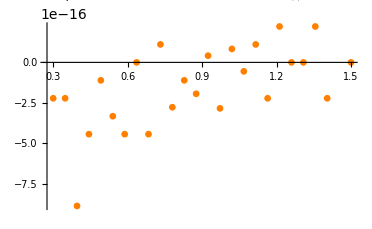

2.04404×10^-30

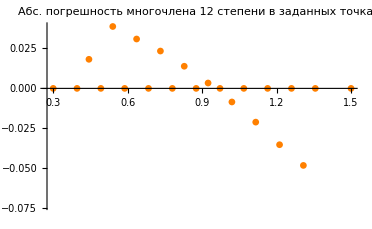

0.0297677

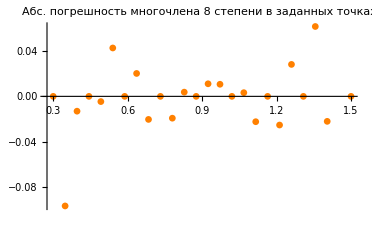

0.0189048

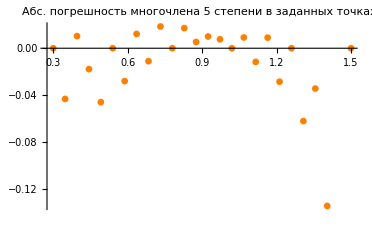

0.0305362

0.0297677

-Graphics-

0.0189048

-Graphics-

0.0305362

```mathematica
Show[ListPlot[difffor24, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 24 степени в заданных точках"]
polynomialfor24S = Sum[((polynomial/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[difffor12, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 12 степени в заданных точках"]
polynomialfor12S = Sum[((polynomialfor12/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[difffor8 , PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 8 степени в заданных точках"]
polynomialfor8S = Sum[((polynomialfor8/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[difffor5, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 5 степени в заданных точках"]
polynomialfor5S = Sum[((polynomialfor5/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
```

Таким образом, наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался многочлен 24-й степени. По графикам можно заметить, что погрешность увеличивается ближе к крайним значениям интерполируемой функции .  Несмотря на это, интерполяция не гарантирует, что поведение полученной функции между узлами интерполяции будет повторять поведение исходной функции. Об этом свидетельствует увеличение погрешности в узлах, которые не были выбраны для интерполяции 12, 8 и 5 степеней.

### Задание 2

```mathematica
splinefor5:=Interpolation[datasetTablefor5,x,Method->"Spline"]
splinePlot5 = Plot[splinefor5, {x,1,2}, PlotStyle->{Red}];
splinefor8:=Interpolation[datasetTablefor8,x,Method->"Spline"]
splinePlot8 = Plot[splinefor8, {x,1,2}, PlotStyle->{Blue}];
splinefor12:=Interpolation[datasetTablefor12,x,Method->"Spline"]
splinePlot12 = Plot[splinefor12, {x,1,2}, PlotStyle->{Black}];
splinefor24:=Interpolation[datasetTable,x,Method->"Spline"]
splinePlot24 = Plot[splinefor24, {x,1,2}, PlotStyle->{Gray}];
```

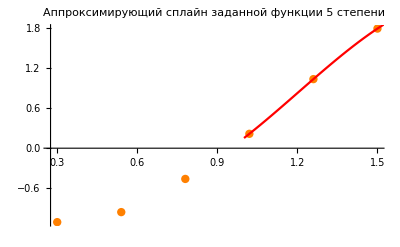

0.0344645

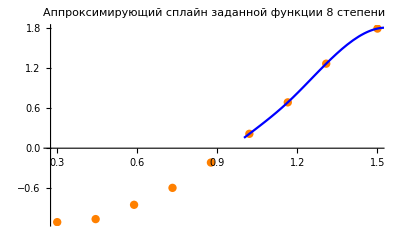

0.0124621

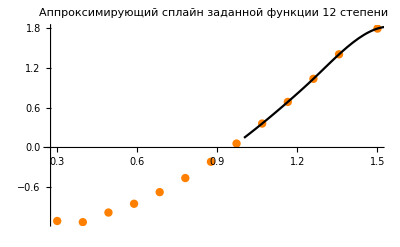

0.0204804

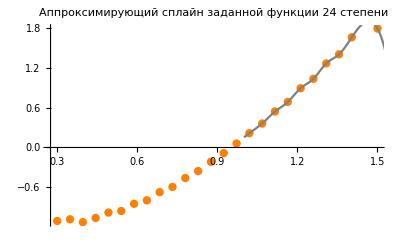

1.94904×10^-31

```mathematica
Show[ListPlot[datasetTablefor5, PlotStyle->{PointSize[0.015],Orange}],splinePlot5, PlotLabel->"Аппроксимирующий сплайн заданной функции 5 степени"]
spline5S =Sum[((splinefor5/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[datasetTablefor8, PlotStyle->{PointSize[0.015],Orange}],splinePlot8,PlotLabel->"Аппроксимирующий сплайн заданной функции 8 степени"]
spline8S =Sum[((splinefor8/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[datasetTablefor12, PlotStyle->{PointSize[0.015],Orange}],splinePlot12, PlotLabel->"Аппроксимирующий сплайн заданной функции 12 степени"]
spline12S =Sum[((splinefor12/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
Show[ListPlot[datasetTable, PlotStyle->{PointSize[0.015],Orange}],splinePlot24, PlotLabel->"Аппроксимирующий сплайн заданной функции 24 степени"]
spline24S =Sum[((splinefor24/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
```

Таким образом, наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался сплайн 24 - й степени . Погрешность оказалась меньше, чем в случае интерполяционного многочлена из задания 1.

### Задание 3

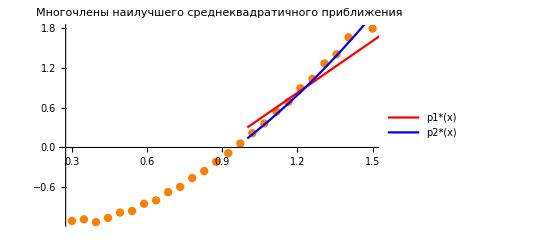

```mathematica
p1=Fit[datasetTable,{1,x},x];
p2=Fit[datasetTable,{1,x, x^2},x];
pPlot = Plot[{p1,p2}, {x,1,2},PlotStyle->{Red, Blue}, PlotLegends->{"p1*(x)","p2*(x)"}];
Show[ListPlot[datasetTable, PlotStyle->{PointSize[0.015],Orange}],pPlot, PlotLabel->"Многочлены наилучшего
cреднеквадратичного приближения"]
```

```mathematica
s1 = Sum[((p1/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
s2 = Sum[((p2/.x->dataset[[i,1]])-dataset[[i,2]])^2, {i,dots}]
```

0.802043

0.0843563

Таким образом, многочлен наилучшего cреднеквадратичного приближения второго порядка показал лучшую точность как графически, так и исходя из высчитанной суммы квадратов разностей

### Задание 4

#### Метод левых прямоугольников

```mathematica
leftRectangle=h*∑_(i=1)^(dots-1) dataset[[i,2]]
```

-0.106319

#### Метод правых прямоугольников

```mathematica
rightRectangle=h*∑_(i=2)^dots dataset[[i,2]]
```

0.0325621

#### Метод средних прямоугольников

```mathematica
avrRectangle=h*∑_(i=1)^(dots-1) (dataset[[i,2]]+dataset[[i+1,2]])/2
```

-0.0368783

#### Метод трапеций

```mathematica
trap=h*∑_(i=1)^(dots-1) (dataset[[i,2]]+dataset[[i+1,2]])/2
```

-0.0368783

#### Метод Симпсона

```mathematica
n = 12;
h = (b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=dataset[[i+1,2]];]
simp=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
Clear[h]
```

-0.0374413

Таким образом, методы правых и левых прямоугольников могут давать завышенные или заниженные результаты в зависимости от производной исходной функции . Методы трапеций и Симпсона позволяют получить более точный результат .

### Задание 5

#### Первая производная (1 порядок точности)

```mathematica
h=0.048;
FDFA=Table[{i,dataset[[i,1]],(dataset[[i+1,2]]-dataset[[i,2]])/h},{i,1,dots-1}]; 
TableForm[FDFA,TableHeadings->{None,{"Узел","x_i","y'_i"}}, ]
```

Узел | x_i | y'_i
1 | 0.3 | 0.526875
2 | 0.348 | -0.88625
3 | 0.396 | 1.305
4 | 0.444 | 1.70006
5 | 0.492 | 0.47475
6 | 0.54 | 2.27625
7 | 0.588 | 1.06829
8 | 0.636 | 2.57367
9 | 0.684 | 1.63265
10 | 0.732 | 2.78269
11 | 0.78 | 2.17879
12 | 0.828 | 2.91981
13 | 0.876 | 2.71369
14 | 0.924 | 2.99694
15 | 0.972 | 3.242
16 | 1.02 | 3.02273
17 | 1.068 | 3.76704
18 | 1.116 | 3.00438
19 | 1.164 | 4.29073
20 | 1.212 | 2.94679
21 | 1.26 | 4.815
22 | 1.308 | 2.85437
23 | 1.356 | 5.34125
24 | 1.404 | 2.73063

#### Первая производная (2 порядок точности)

```mathematica
FDSA=Table[{i,dataset[[i,1]],(dataset[[i+1,2]]-dataset[[i-1,2]])/(2*h)},{i,2,dots-1}]; 
TableForm[FDSA,TableHeadings->{None,{"Узел","x_i","y'_i"}}, ]
```

Узел | x_i | y'_i
2 | 0.348 | -0.179687
3 | 0.396 | 0.209375
4 | 0.444 | 1.50253
5 | 0.492 | 1.08741
6 | 0.54 | 1.3755
7 | 0.588 | 1.67227
8 | 0.636 | 1.82098
9 | 0.684 | 2.10316
10 | 0.732 | 2.20767
11 | 0.78 | 2.48074
12 | 0.828 | 2.5493
13 | 0.876 | 2.81675
14 | 0.924 | 2.85531
15 | 0.972 | 3.11947
16 | 1.02 | 3.13236
17 | 1.068 | 3.39489
18 | 1.116 | 3.38571
19 | 1.164 | 3.64755
20 | 1.212 | 3.61876
21 | 1.26 | 3.8809
22 | 1.308 | 3.83469
23 | 1.356 | 4.09781
24 | 1.404 | 4.03594

#### Вторая производная (2 порядок точности)

```mathematica
SDSA=Table[{i,dataset[[i,1]],(dataset[[i+1,2]]-2*dataset[[i,2]]+dataset[[i-1,2]])/h^2},{i,2,dots-1}]; 
TableForm[SDSA,TableHeadings->{None,{"Узел","x_i","y('')_i"}}, ]
```

Узел | x_i | y('')_i
2 | 0.348 | -29.4401
3 | 0.396 | 45.651
4 | 0.444 | 8.23047
5 | 0.492 | -25.5273
6 | 0.54 | 37.5313
7 | 0.588 | -25.1658
8 | 0.636 | 31.362
9 | 0.684 | -19.6046
10 | 0.732 | 23.9592
11 | 0.78 | -12.5812
12 | 0.828 | 15.4379
13 | 0.876 | -4.29431
14 | 0.924 | 5.90117
15 | 0.972 | 5.10534
16 | 1.02 | -4.5681
17 | 1.068 | 15.5065
18 | 1.116 | -15.8889
19 | 1.164 | 26.799
20 | 1.212 | -27.9987
21 | 1.26 | 38.921
22 | 1.308 | -40.8464
23 | 1.356 | 51.8099
24 | 1.404 | -54.388

Таким образом, использование формул численного дифференцирования может дать удовлетворительные результаты для нахождения производных 1 и 2 порядка . Однако при шаге сетки, близком к нулю, неустранимые погрешности в значениях функции оказывают сильное влияние на результат (замечание из лекции 10), о чём свидетельствуют вычисленные значения 2 - й производной .